# SpectralGapAsymptotics

## Higher-order asymptotics of the logarithmic spectral gap

## Purpose

This notebook supports the spectral-gap asymptotics studied in Chapter 4. It computes the exact logarithmic gap, derives its first three even-power asymptotic coefficients, studies scaled residuals, and compares analytic coefficients with numerical fits.

All executable cells are ordinary Wolfram Language Input cells. Typeset box expressions appear only in explanatory cells.

## 1. Exact spectral gap

```mathematica
ClearAll["Global`*"];

lambda[n_Integer?Positive, k_Integer, alpha_] :=
  (1 - alpha) + alpha Exp[2 Pi I k/n];

muSquared[n_Integer?Positive, k_Integer, alpha_] :=
  1 - 2 alpha (1 - alpha) (1 - Cos[2 Pi k/n]);

mu[n_Integer?Positive, k_Integer, alpha_?NumericQ] :=
  Sqrt[muSquared[n, k, alpha]];

gamma[n_Integer?Positive, alpha_?NumericQ] :=
  (1/2) Log[muSquared[n, 1, alpha]/muSquared[n, 2, alpha]];
```

γ_n(α)=1/2 log((1-2α(1-α)(1-cos((2π)/n)))/(1-2α(1-α)(1-cos((4π)/n))))

```mathematica
alphaExample = 0.35;
Table[{n, gamma[n, alphaExample]}, {n, 5, 30}] // TableForm
```

5 | 0.677365
6 | 0.444577
7 | 0.312288
8 | 0.231973
9 | 0.179518
10 | 0.143275
11 | 0.117128
12 | 0.0976139
13 | 0.0826457
14 | 0.0709029
15 | 0.0615148
16 | 0.0538874
17 | 0.047604
18 | 0.0423647
19 | 0.0379493
20 | 0.0341929
21 | 0.0309702
22 | 0.0281842
23 | 0.0257592
24 | 0.0236352
25 | 0.0217642
26 | 0.0201075
27 | 0.0186335
28 | 0.0173163
29 | 0.0161342
30 | 0.0150694

## 2. Symbolic expansion variable

```mathematica
q[alpha_] := alpha (1 - alpha);
```

Writing q=α(1-α), the expansion has only even powers of 1/n.

## 3. First three asymptotic coefficients

```mathematica
c2[alpha_] :=
  6 Pi^2 q[alpha];

c4[alpha_] :=
  Pi^4 (60 q[alpha]^2 - 10 q[alpha]);

c6[alpha_] :=
  Pi^6 (672 q[alpha]^3 - 168 q[alpha]^2 + (28/5) q[alpha]);
```

γ_n(α)=C_2/n^2+C_4/n^4+C_6/n^6+O(n^-8)

```mathematica
{c2[alphaExample], c4[alphaExample], c6[alphaExample]} // N
```

{13.472,80.8861,472.47}

## 4. Truncated asymptotic models

```mathematica
gapOrder2[n_Integer?Positive, alpha_?NumericQ] :=
  c2[alpha]/n^2;

gapOrder4[n_Integer?Positive, alpha_?NumericQ] :=
  c2[alpha]/n^2 + c4[alpha]/n^4;

gapOrder6[n_Integer?Positive, alpha_?NumericQ] :=
  c2[alpha]/n^2 + c4[alpha]/n^4 + c6[alpha]/n^6;
```

```mathematica
Table[
  {
    n,
    gamma[n, alphaExample],
    gapOrder2[n, alphaExample],
    gapOrder4[n, alphaExample],
    gapOrder6[n, alphaExample]
  },
  {n, 20, 200, 20}
] // TableForm
```

20 | 0.0341929 | 0.03368 | 0.0341856 | 0.0341929
40 | 0.00845172 | 0.00842001 | 0.0084516 | 0.00845172
60 | 0.00374848 | 0.00374223 | 0.00374847 | 0.00374848
80 | 0.00210698 | 0.002105 | 0.00210698 | 0.00210698
100 | 0.00134801 | 0.0013472 | 0.00134801 | 0.00134801
120 | 0.000935946 | 0.000935556 | 0.000935946 | 0.000935946
140 | 0.000687558 | 0.000687347 | 0.000687558 | 0.000687558
160 | 0.000526374 | 0.00052625 | 0.000526374 | 0.000526374
180 | 0.00041588 | 0.000415803 | 0.00041588 | 0.00041588
200 | 0.000336851 | 0.0003368 | 0.000336851 | 0.000336851

## 5. Leading scaled gap

The leading prediction is

n^2 γ_n(α)→6 π^2 α(1-α)

```mathematica
scaledGap2[n_Integer?Positive, alpha_?NumericQ] :=
  n^2 gamma[n, alpha];

Table[
  {n, scaledGap2[n, alphaExample], c2[alphaExample]},
  {n, 20, 300, 20}
] // TableForm
```

20 | 13.6772 | 13.472
40 | 13.5227 | 13.472
60 | 13.4945 | 13.472
80 | 13.4847 | 13.472
100 | 13.4801 | 13.472
120 | 13.4776 | 13.472
140 | 13.4761 | 13.472
160 | 13.4752 | 13.472
180 | 13.4745 | 13.472
200 | 13.474 | 13.472
220 | 13.4737 | 13.472
240 | 13.4734 | 13.472
260 | 13.4732 | 13.472
280 | 13.473 | 13.472
300 | 13.4729 | 13.472

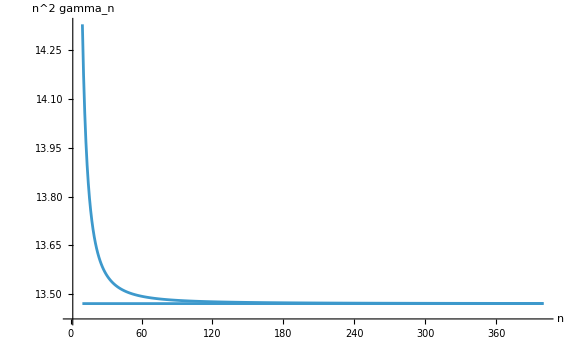

```mathematica
Show[
  ListLinePlot[
    Table[{n, scaledGap2[n, alphaExample]}, {n, 10, 400}],
    AxesLabel -> {"n", "n^2 gamma_n"},
    PlotRange -> All
  ],
  Plot[c2[alphaExample], {n, 10, 400}],
  ImageSize -> Large
]
```

## 6. The n^-4 correction

n^4(γ_n-C_2/n^2)→C_4

```mathematica
scaledResidual4[n_Integer?Positive, alpha_?NumericQ] :=
  n^4 (gamma[n, alpha] - c2[alpha]/n^2);

Table[
  {n, scaledResidual4[n, alphaExample], c4[alphaExample]},
  {n, 20, 300, 20}
] // TableForm
```

20 | 82.0675 | 80.8861
40 | 81.1814 | 80.8861
60 | 81.0173 | 80.8861
80 | 80.9599 | 80.8861
100 | 80.9333 | 80.8861
120 | 80.9189 | 80.8861
140 | 80.9102 | 80.8861
160 | 80.9045 | 80.8861
180 | 80.9007 | 80.8861
200 | 80.8979 | 80.8861
220 | 80.8958 | 80.8861
240 | 80.8943 | 80.8861
260 | 80.8931 | 80.8861
280 | 80.8921 | 80.8861
300 | 80.8913 | 80.8861

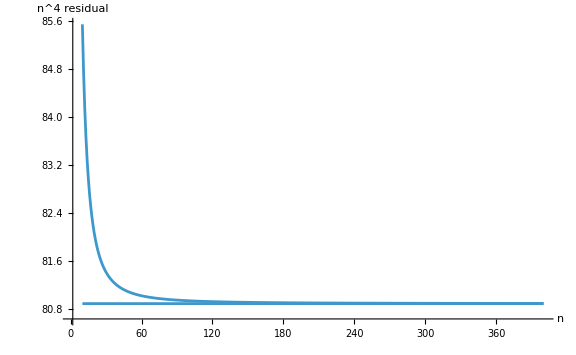

```mathematica
Show[
  ListLinePlot[
    Table[{n, scaledResidual4[n, alphaExample]}, {n, 10, 400}],
    AxesLabel -> {"n", "n^4 residual"},
    PlotRange -> All
  ],
  Plot[c4[alphaExample], {n, 10, 400}],
  ImageSize -> Large
]
```

## 7. The n^-6 correction

n^6(γ_n-C_2/n^2-C_4/n^4)→C_6

```mathematica
scaledResidual6[n_Integer?Positive, alpha_?NumericQ] :=
  n^6 (gamma[n, alpha] - c2[alpha]/n^2 - c4[alpha]/n^4);

Table[
  {n, scaledResidual6[n, alphaExample], c6[alphaExample]},
  {n, 20, 300, 20}
] // TableForm
```

20 | 472.558 | 472.47
40 | 472.572 | 472.47
60 | 472.522 | 472.47
80 | 472.501 | 472.47
100 | 472.49 | 472.47
120 | 472.484 | 472.47
140 | 472.481 | 472.47
160 | 472.478 | 472.47
180 | 472.48 | 472.47
200 | 472.472 | 472.47
220 | 472.481 | 472.47
240 | 472.486 | 472.47
260 | 472.464 | 472.47
280 | 472.425 | 472.47
300 | 472.483 | 472.47

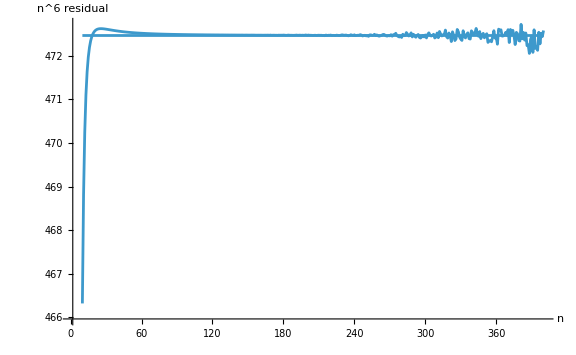

```mathematica
Show[
  ListLinePlot[
    Table[{n, scaledResidual6[n, alphaExample]}, {n, 10, 400}],
    AxesLabel -> {"n", "n^6 residual"},
    PlotRange -> All
  ],
  Plot[c6[alphaExample], {n, 10, 400}],
  ImageSize -> Large
]
```

## 8. Relative errors by truncation order

```mathematica
relativeError[exact_, approximation_] :=
  Abs[exact - approximation]/Abs[exact];

errorTable = Table[
  {
    n,
    relativeError[gamma[n, alphaExample], gapOrder2[n, alphaExample]],
    relativeError[gamma[n, alphaExample], gapOrder4[n, alphaExample]],
    relativeError[gamma[n, alphaExample], gapOrder6[n, alphaExample]]
  },
  {n, 10, 300, 10}
];
errorTable // TableForm
```

10 | 0.0597098 | 0.00325468 | 0.0000429676
20 | 0.0150008 | 0.000215943 | 3.99241×10^-8
30 | 0.00666965 | 0.0000430214 | 1.32595×10^-8
40 | 0.00375208 | 0.000013651 | 2.94713×10^-9
50 | 0.00240144 | 5.59865×10^-6 | 8.42924×10^-10
60 | 0.0016677 | 2.70184×10^-6 | 2.94999×10^-10
70 | 0.00122527 | 1.45899×10^-6 | 1.20021×10^-10
80 | 0.000938102 | 8.55465×10^-7 | 5.47283×10^-11
90 | 0.00074122 | 5.34161×10^-7 | 2.72943×10^-11
100 | 0.000600391 | 3.50509×10^-7 | 1.45708×10^-11
110 | 0.000496192 | 2.39426×10^-7 | 8.36281×10^-12
120 | 0.00041694 | 1.69063×10^-7 | 4.94406×10^-12
130 | 0.000355263 | 1.22751×10^-7 | 3.05637×10^-12
140 | 0.000306324 | 9.12655×10^-8 | 1.97553×10^-12
150 | 0.000266843 | 6.92579×10^-8 | 1.28258×10^-12
160 | 0.00023453 | 5.35016×10^-8 | 8.24315×10^-13
170 | 0.00020775 | 4.19818×10^-8 | 4.80763×10^-13
180 | 0.000185308 | 3.34026×10^-8 | 6.55663×10^-13
190 | 0.000166315 | 2.69067×10^-8 | 3.21704×10^-13
200 | 0.0001501 | 2.19159×10^-8 | 7.46725×10^-14
210 | 0.000136145 | 1.80307×10^-8 | 2.38289×10^-13
220 | 0.000124049 | 1.49695×10^-8 | 3.31046×10^-13
230 | 0.000113497 | 1.25313×10^-8 | 3.74174×10^-13
240 | 0.000104236 | 1.05698×10^-8 | 3.45428×10^-13
250 | 0.0000960639 | 8.977×10^-9 | 1.88477×10^-13
260 | 0.0000888165 | 7.6737×10^-9 | 1.00501×10^-13
270 | 0.0000823593 | 6.59847×10^-9 | 1.19234×10^-13
280 | 0.0000765816 | 5.70473×10^-9 | 5.43205×10^-13
290 | 0.0000713912 | 4.95844×10^-9 | 2.98118×10^-13
300 | 0.0000667111 | 4.32952×10^-9 | 1.11535×10^-13

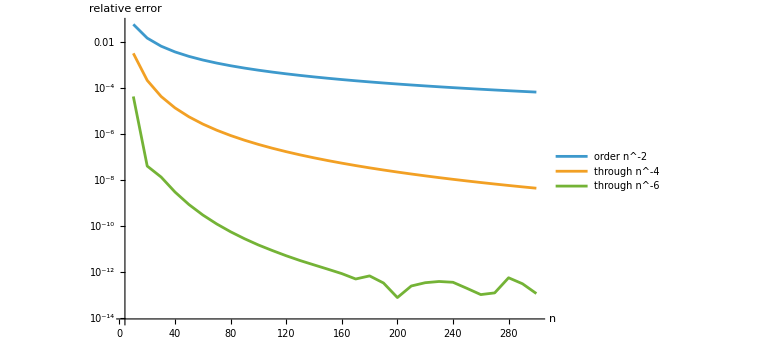

```mathematica
ListLogPlot[
  {
    errorTable[[All, {1, 2}]],
    errorTable[[All, {1, 3}]],
    errorTable[[All, {1, 4}]]
  },
  Joined -> True,
  PlotLegends -> {"order n^-2", "through n^-4", "through n^-6"},
  AxesLabel -> {"n", "relative error"},
  PlotRange -> All,
  ImageSize -> Large
]
```

## 9. Numerical coefficient fitting

```mathematica
fitCoefficients[alpha_?NumericQ, nMin_Integer?Positive, nMax_Integer?Positive] := Module[
  {data, fit},
  data = Table[
    {1/n^2, gamma[n, alpha]},
    {n, nMin, nMax}
  ];
  fit = LinearModelFit[data, {x, x^2, x^3}, x, IncludeConstantBasis -> False];
  fit["BestFitParameters"]
];
```

```mathematica
fittedCoefficients = fitCoefficients[alphaExample, 80, 400];
analyticCoefficients = {c2[alphaExample], c4[alphaExample], c6[alphaExample]};
{N[fittedCoefficients], N[analyticCoefficients]}
```

{{13.472,80.8861,472.52},{13.472,80.8861,472.47}}

```mathematica
fitCoefficientErrors = Abs[N[fittedCoefficients - analyticCoefficients]];
fitCoefficientErrors
```

{6.71463×10^-11,3.60061×10^-6,0.0496679}

## 10. Dependence on alpha

```mathematica
alphaGrid = Range[0.05, 0.95, 0.05];
coefficientData = Table[
  {alpha, c2[alpha], c4[alpha], c6[alpha]},
  {alpha, alphaGrid}
];
```

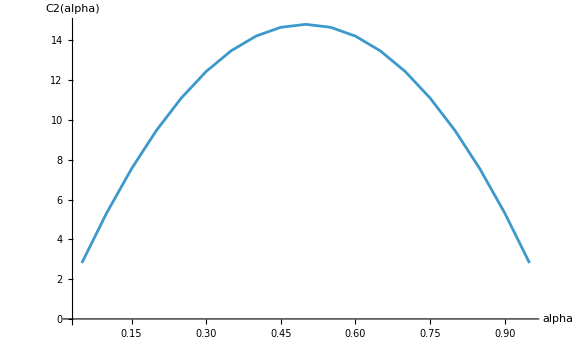

```mathematica
ListLinePlot[
  coefficientData[[All, {1, 2}]],
  AxesLabel -> {"alpha", "C2(alpha)"},
  PlotRange -> All,
  ImageSize -> Large
]
```

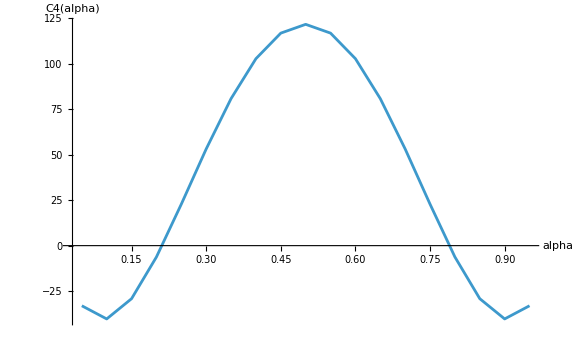

```mathematica
ListLinePlot[
  coefficientData[[All, {1, 3}]],
  AxesLabel -> {"alpha", "C4(alpha)"},
  PlotRange -> All,
  ImageSize -> Large
]
```

## 11. Symmetry about alpha = 1/2

```mathematica
coefficientSymmetryError[coefficient_, alpha_?NumericQ] :=
  Abs[N[coefficient[alpha] - coefficient[1 - alpha]]];

Table[
  {
    alpha,
    coefficientSymmetryError[c2, alpha],
    coefficientSymmetryError[c4, alpha],
    coefficientSymmetryError[c6, alpha]
  },
  {alpha, {0.1, 0.2, 0.3, 0.4}}
] // TableForm
```

0.1 | 8.88178×10^-16 | 0. | 2.84217×10^-13
0.2 | 3.55271×10^-15 | 6.4837×10^-14 | 0.
0.3 | 1.77636×10^-15 | 8.52651×10^-14 | 0.
0.4 | 0. | 0. | 0.

## 12. Optimal leading coefficient

The leading coefficient is maximal at α=1/2.

```mathematica
optimalLeadingCoefficient = NMaximize[
  {c2[alpha], 0 < alpha < 1},
  alpha
];
optimalLeadingCoefficient
```

{14.8044,{alpha→0.5}}

## 13. Effective convergence exponents

```mathematica
effectiveExponent[data_List] := Module[{pairs},
  pairs = Partition[data, 2, 1];
  Table[
    -Log[pair[[2, 2]]/pair[[1, 2]]]/Log[pair[[2, 1]]/pair[[1, 1]]],
    {pair, pairs}
  ]
];

order2Errors = Table[
  {n, Abs[gamma[n, alphaExample] - gapOrder2[n, alphaExample]]},
  {n, 30, 300, 10}
];

order4Errors = Table[
  {n, Abs[gamma[n, alphaExample] - gapOrder4[n, alphaExample]]},
  {n, 30, 300, 10}
];
```

```mathematica
{
  Mean[Take[effectiveExponent[order2Errors], -8]],
  Mean[Take[effectiveExponent[order4Errors], -8]]
}
```

{4.00018,5.99996}

## 14. Suppression-time asymptotics

```mathematica
suppressionTimeExact[n_Integer?Positive, alpha_?NumericQ, C_?Positive, epsilon_?Positive] :=
  Log[C/epsilon]/gamma[n, alpha];

suppressionTimeLeading[n_Integer?Positive, alpha_?NumericQ, C_?Positive, epsilon_?Positive] :=
  Log[C/epsilon] n^2/c2[alpha];
```

```mathematica
Table[
  {
    n,
    suppressionTimeExact[n, alphaExample, 2., 10^-3],
    suppressionTimeLeading[n, alphaExample, 2., 10^-3],
    suppressionTimeExact[n, alphaExample, 2., 10^-3]/n^2
  },
  {n, 20, 200, 20}
] // TableForm
```

20 | 222.294 | 225.68 | 0.555736
40 | 899.332 | 902.719 | 0.562083
60 | 2027.73 | 2031.12 | 0.563259
80 | 3607.49 | 3610.88 | 0.56367
100 | 5638.61 | 5642. | 0.563861
120 | 8121.09 | 8124.47 | 0.563964
140 | 11054.9 | 11058.3 | 0.564027
160 | 14440.1 | 14443.5 | 0.564067
180 | 18276.7 | 18280.1 | 0.564095
200 | 22564.6 | 22568. | 0.564115

## 15. Automated verification report

```mathematica
Clear[verificationReport];

verificationReport[] := verificationReport[12];

verificationReport[count_Integer?Positive] := Module[{rows, alphaValues},
  alphaValues = Subdivide[0.1, 0.9, count - 1];
  rows = Table[
    Module[{n, r2, r4, r6, symmetryError, fit, analytic, fitError},
      n = 600;
      r2 = Abs[N[scaledGap2[n, alpha] - c2[alpha]]];
      r4 = Abs[N[scaledResidual4[n, alpha] - c4[alpha]]];
      r6 = Abs[N[scaledResidual6[n, alpha] - c6[alpha]]];
      symmetryError = Max[{
        coefficientSymmetryError[c2, alpha],
        coefficientSymmetryError[c4, alpha],
        coefficientSymmetryError[c6, alpha]
      }];
      fit = fitCoefficients[alpha, 100, 500];
      analytic = {c2[alpha], c4[alpha], c6[alpha]};
      fitError = Max[Abs[N[fit - analytic]]];
      <|
        "alpha" -> alpha,
        "C2 scaled limit" -> TrueQ[r2 < 10^-4],
        "C4 scaled limit" -> TrueQ[r4 < 10^-2],
        "C6 scaled limit" -> TrueQ[r6 < 2],
        "Alpha symmetry" -> TrueQ[symmetryError < 10^-10],
        "Coefficient fit" -> TrueQ[fitError < 1]
      |>
    ],
    {alpha, alphaValues}
  ];
  Dataset[rows]
];
```

```mathematica
verificationReport[]
```

## Conclusion

The numerical experiments confirm the even-power expansion of the logarithmic spectral gap. The leading term is of order n^-2, while subtracting successive analytic terms reveals stable n^-4 and n^-6 corrections. The fitted coefficients agree with the analytic formulas and inherit the symmetry .